```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
g[x_]:=Quiet[NIntegrate[(2 p)/(p^2+1)Sinc[p x],{p,0,∞},MaxRecursion->50,WorkingPrecision->30,PrecisionGoal->30]];
```

```mathematica
Integrate[(2 p)/(p^2+1)Sinc[p x],{p,0,∞}]//FullSimplify
```

ConditionalExpression[1/2 √π MeijerG[{{0},{}},{{0,0},{-1/2}},x^2/4],x∈Reals]

```mathematica
Limit[1/2 √π MeijerG[{{0},{}},{{0,0},{-1/2}},x^2/4],x->∞]
```

0

```mathematica
Assuming[Element[x,Reals],y1[x] x^2 1/2 √π MeijerG[{{0},{}},{{0,0},{-1/2}},x^2/4]]//FullSimplify
```

2 √π x BesselI[2/5,(2 x^(5/2))/5] MeijerG[{{1},{}},{{1,1},{1/2}},x^2/4]

```mathematica
Integrate[MeijerG[{{1},{}},{{1,1},{1/2}},x^2/4],x]
```

1/2 x MeijerG[{{1},{}},{{1,1},{-1/2}},x^2/4]

```mathematica
D[MeijerG[{{1},{}},{{1,1},{1/2}},x^2/4],x]
```

1/2 x MeijerG[{{-1},{}},{{0,0},{-1/2}},x^2/4]

```mathematica
Integrate[2 √π x BesselI[2/5,(2 x^(5/2))/5],x]
```

(2 √π x^2 (x^(5/2))^(2/5) Gamma[3/5] HypergeometricPFQ[{3/5},{7/5,8/5},x^5/25])/(5 5^(2/5) Gamma[7/5] Gamma[8/5])

```mathematica
D[2 √π x BesselI[2/5,(2 x^(5/2))/5],x]
```

2 √π BesselI[2/5,(2 x^(5/2))/5]+√π x^(5/2) (BesselI[-3/5,(2 x^(5/2))/5]+BesselI[7/5,(2 x^(5/2))/5])

```mathematica
Limit[1/2 √π x^3 MeijerG[{{0},{}},{{0,0},{-1/2}},x^2/4],x->∞]
```

∞

```mathematica
g[0.0001]
```

19.2662494490374931413081460281

```mathematica
N[1/2 √π MeijerG[{{0},{}},{{0,0},{-1/2}},x^2/4]/.x->0.0001,50]
```

19.2662

```mathematica
g2Tab=Quiet[Join[ParallelTable[{x,x^2 g[x]},{x,10^-9,10^-4,10^-7}],ParallelTable[{x,x^2 g[x]},{x,10^-4+10^-3,10^-1,10^-3}],ParallelTable[{x,x^2 g[x]},{x,10^-1+10^-2,2,10^-2}],ParallelTable[{x,x^2 g[x]},{x,2.1,10,0.1}],ParallelTable[{x,x^2 g[x]},{x,10.5,100,0.5}],ParallelTable[{x,x^2 g[x]},{x,110,1000,10}]]];
```

```mathematica
g2Inter=Interpolation[g2Tab];
```

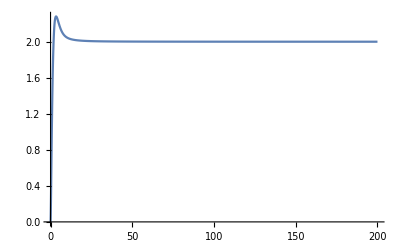

```mathematica
Plot[g2Inter[x],{x,0,200},PlotRange->All]
```

## Fundamental Solution

```mathematica
DSolve[f''[x]-1/x f'[x]-x^3 f[x]==0,f[x],x]
```

{{f[x]→(x BesselI[-2/5,(2 x^(5/2))/5] C[1] Gamma[3/5])/5^(2/5)+(-1/5)^(2/5) x BesselI[2/5,(2 x^(5/2))/5] C[2] Gamma[7/5]}}

```mathematica
u1[x_]:=x BesselI[-2/5,(2 x^(5/2))/5];
```

```mathematica
u1''[x]-1/x u1'[x]-x^3 u1[x]//FullSimplify
```

0

```mathematica
u2[x_]:=x BesselI[2/5,(2 x^(5/2))/5];
```

```mathematica
u2''[x]-1/x u2'[x]-x^3 u2[x]//FullSimplify
```

0

## Homogeneous Solution with BCs

### BC1 : y'[0] = y[0]=0

```mathematica
D[u1[x],x]
```

BesselI[-2/5,(2 x^(5/2))/5]+1/2 x^(5/2) (BesselI[-7/5,(2 x^(5/2))/5]+BesselI[3/5,(2 x^(5/2))/5])

```mathematica
Limit[D[u1[x],x],x->0]
```

0

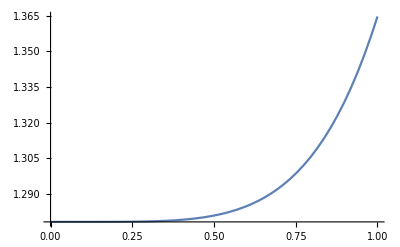

```mathematica
Plot[u1[x],{x,0,1},PlotRange->All]
```

```mathematica
Limit[u1[x],x->0]
```

5^(2/5)/Gamma[3/5]

```mathematica
D[u2[x],x]
```

BesselI[2/5,(2 x^(5/2))/5]+1/2 x^(5/2) (BesselI[-3/5,(2 x^(5/2))/5]+BesselI[7/5,(2 x^(5/2))/5])

```mathematica
Limit[D[u2[x],x],x->0]
```

0

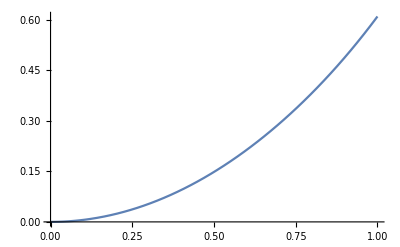

```mathematica
Plot[u2[x],{x,0,1}]
```

```mathematica
u2[0]
```

0

```mathematica
y1[x_]:=u2[x];
```

### BC2 : y'[∞] = 0

```mathematica
Limit[D[u1[x]-u2[x],x],x->∞]
```

0

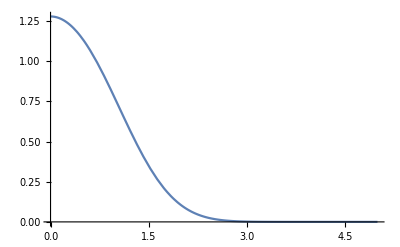

```mathematica
Plot[u1[x]-u2[x],{x,0,5},PlotRange->All]
```

```mathematica
y2[x_]:=u1[x]-u2[x];
```

## Construction of Wronskian

```mathematica
D[y2[x],x]y1[x]-y2[x]D[y1[x],x]//FullSimplify
```

-(5 √(1/2 (5+√5)) x)/(2 π)

```mathematica
W[x_]:=-(5 √(1/2 (5+√5)) x)/(2 π);
```

```mathematica
c=N[(5 √(1/2 (5+√5)))/(2 π)]
```

1.51365

## Construction of Inhomogeneous Solution

```mathematica
y[x_?NumericQ]:=-1/c y2[x]NIntegrate[y1[s]g2Inter[s],{s,10^-9,x},MinRecursion->20,MaxRecursion->50,WorkingPrecision->30,PrecisionGoal->10]-1/c y1[x]NIntegrate[y2[s]g2Inter[s],{s,x,∞},MaxRecursion->50,WorkingPrecision->30,PrecisionGoal->10];
```

```mathematica
y[6]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
yTab=Table[{i,0},{i,0.1,6,0.1}];
SetSharedVariable[yTab];
```

```mathematica
ParallelDo[yTab[[i,2]]=y[yTab[[i,1]]],{i,1,Length[yTab]}]
```

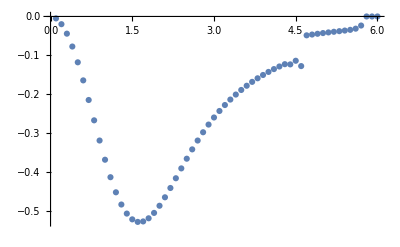

```mathematica
ListPlot[yTab]
```

```mathematica
yTab[[-15]]
```

{4.6,-0.292476}

```mathematica
yInter=Interpolation[yTab[[;;-15]]];
```

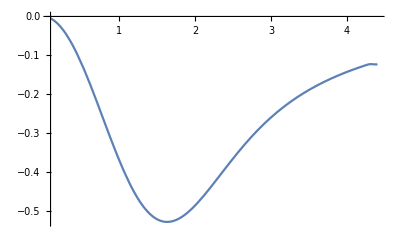

```mathematica
Plot[yInter[x],{x,0.1,4.4}]
```

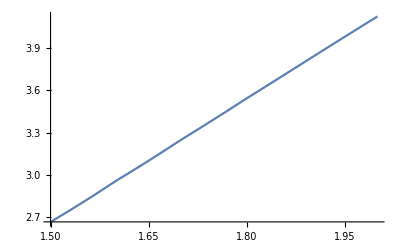

```mathematica
Plot[yInter''[x]-1/x yInter'[x]-x^3 yInter[x],{x,1.5,2}]
```

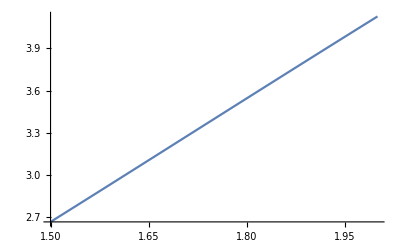

```mathematica
Plot[x^3 g[x],{x,1.5,2}]
```

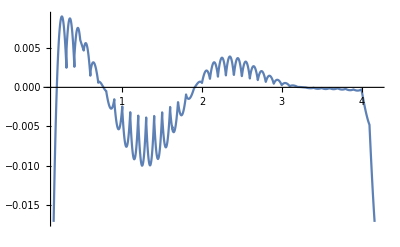

```mathematica
Plot[(yInter''[x]-1/x yInter'[x]-x^3 yInter[x])-(x^3 g[x]),{x,0.1,4.2}]
```